```mathematica
x00t=(k*xtot0*f000*Exp[(r-2*μ)*t])/(k+xtot0*(Exp[r*t]-1));
x1t=(k*xtot0*Exp[(r-2*μ)*t]*(-2*f000+Exp[t*μ]*(f000+1)))/(k+xtot0*(Exp[r*t]-1));
x11t=(k*xtot0*Exp[(r-2*μ)*t]*(Exp[t*μ]-1)*(-f000+Exp[t*μ]))/(k+xtot0*(Exp[r*t]-1));
x00tM=x00t/.t->tM;
x1tM=x1t/.t->tM;
x11tM=x11t/.t->tM;
x00T=x00tM+0.5*x1tM-1/((0.5*x1tM)^-1+α*Pr*(t-tM))//FullSimplify;
x1T=2/((0.5*x1tM)^-1+α*Pr*(t-tM))//FullSimplify;
x11T=x11tM+0.5*x1tM-1/((0.5*x1tM)^-1+α*Pr*(t-tM))//FullSimplify;
changef000=x00T/(x00T+x1T)-f000//FullSimplify;
Numerator[Together[changef000]]//FullSimplify;
Solve[%==0,f000];
f000/.%;
f000=%13[[3]];
```

```mathematica
params={r->2,k->1,t->25,α->0.3,Pr->0.1,μ->0.01};
xhealthy=(ⅇ^(tM (r-μ)) (0.5+0.5 f000) k xtot0)/(k+(-1.+ⅇ^(r tM)) xtot0)+1/((2. ⅇ^(-tM (r-2 μ)) (k+(-1+ⅇ^(r tM)) xtot0))/((-2 f000+ⅇ^(tM μ) (1+f000)) k xtot0)+Pr (t-tM) α)/.params;
dx00x1dtM=D[xhealthy,tM];
f[x0_]:=FindRoot[Re[dx00x1dtM/.params/.xtot0->x0]==0,{tM,3}]
```

```mathematica
Table[f[i],{i,0.01,0.8,0.01}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{tM→4.94421},{tM→4.59256},{tM→4.3847},{tM→4.23568},{tM→4.11887},{tM→4.02242},{tM→3.94},{tM→3.86783},{tM→3.80347},{tM→3.74526},{tM→3.69202},{tM→3.64287},{tM→3.59713},{tM→3.5543},{tM→3.51395},{tM→3.47577},{tM→3.43947},{tM→3.40483},{tM→3.37166},{tM→3.3398},{tM→3.30912},{tM→3.27949},{tM→3.25081},{tM→3.22299},{tM→3.19596},{tM→3.16964},{tM→3.14396},{tM→3.11888},{tM→3.09434},{tM→3.0703},{tM→3.04671},{tM→3.02354},{tM→3.00074},{tM→2.9783},{tM→2.95617},{tM→2.93433},{tM→2.91276},{tM→2.89143},{tM→2.87031},{tM→2.84938},{tM→2.82864},{tM→2.80804},{tM→2.78758},{tM→2.76723},{tM→2.74699},{tM→2.72682},{tM→2.70672},{tM→2.68667},{tM→2.66666},{tM→2.64665},{tM→2.62665},{tM→2.60663},{tM→2.58658},{tM→2.56648},{tM→2.54632},{tM→2.52607},{tM→2.50573},{tM→2.48527},{tM→2.46467},{tM→2.44392},{tM→2.423},{tM→2.40188},{tM→2.38054},{tM→2.35897},{tM→2.33713},{tM→2.31501},{tM→2.29256},{tM→2.26977},{tM→2.24659},{tM→2.223},{tM→2.19896},{tM→2.17442},{tM→2.14934},{tM→2.12367},{tM→2.09735},{tM→2.07031},{tM→2.0425},{tM→2.01382},{tM→1.98419},{tM→1.95351}}

```mathematica
Table[%[[i,1,2]],{i,1,Length[%]}]
```

{4.94421,4.59256,4.3847,4.23568,4.11887,4.02242,3.94,3.86783,3.80347,3.74526,3.69202,3.64287,3.59713,3.5543,3.51395,3.47577,3.43947,3.40483,3.37166,3.3398,3.30912,3.27949,3.25081,3.22299,3.19596,3.16964,3.14396,3.11888,3.09434,3.0703,3.04671,3.02354,3.00074,2.9783,2.95617,2.93433,2.91276,2.89143,2.87031,2.84938,2.82864,2.80804,2.78758,2.76723,2.74699,2.72682,2.70672,2.68667,2.66666,2.64665,2.62665,2.60663,2.58658,2.56648,2.54632,2.52607,2.50573,2.48527,2.46467,2.44392,2.423,2.40188,2.38054,2.35897,2.33713,2.31501,2.29256,2.26977,2.24659,2.223,2.19896,2.17442,2.14934,2.12367,2.09735,2.07031,2.0425,2.01382,1.98419,1.95351}

```mathematica
g[x0_]:=FindRoot[Re[dx00x1dtM/.params/.xtot0->x0]==0,{tM,1}]
Table[g[i],{i,0.8,0.99,0.01}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{tM→1.95351},{tM→1.92165},{tM→1.88848},{tM→1.85384},{tM→1.81754},{tM→1.77935},{tM→1.73901},{tM→1.69617},{tM→1.65044},{tM→1.60128},{tM→1.54804},{tM→1.48983},{tM→1.42548},{tM→1.35331},{tM→1.27088},{tM→1.17443},{tM→1.05763},{tM→0.908603},{tM→0.700742},{tM→0.349092}}

```mathematica
Table[%[[i,1,2]],{i,1,Length[%]}]
```

{1.95351,1.92165,1.88848,1.85384,1.81754,1.77935,1.73901,1.69617,1.65044,1.60128,1.54804,1.48983,1.42548,1.35331,1.27088,1.17443,1.05763,0.908603,0.700742,0.349092}

```mathematica
Join[%20,%23];
```

```mathematica
%24
```

{4.94421,4.59256,4.3847,4.23568,4.11887,4.02242,3.94,3.86783,3.80347,3.74526,3.69202,3.64287,3.59713,3.5543,3.51395,3.47577,3.43947,3.40483,3.37166,3.3398,3.30912,3.27949,3.25081,3.22299,3.19596,3.16964,3.14396,3.11888,3.09434,3.0703,3.04671,3.02354,3.00074,2.9783,2.95617,2.93433,2.91276,2.89143,2.87031,2.84938,2.82864,2.80804,2.78758,2.76723,2.74699,2.72682,2.70672,2.68667,2.66666,2.64665,2.62665,2.60663,2.58658,2.56648,2.54632,2.52607,2.50573,2.48527,2.46467,2.44392,2.423,2.40188,2.38054,2.35897,2.33713,2.31501,2.29256,2.26977,2.24659,2.223,2.19896,2.17442,2.14934,2.12367,2.09735,2.07031,2.0425,2.01382,1.98419,1.95351,1.95351,1.92165,1.88848,1.85384,1.81754,1.77935,1.73901,1.69617,1.65044,1.60128,1.54804,1.48983,1.42548,1.35331,1.27088,1.17443,1.05763,0.908603,0.700742,0.349092}

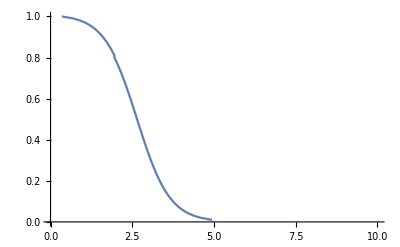

```mathematica
ListLinePlot[Transpose[{%25,0.01*Range[100]}],PlotRange->{{0,10},{0,1}}]
```

```mathematica
a=Export["tMstarvec.mat",%74];
```

```mathematica
Save[a,"a"]
```